```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 1

### Explicit Euler

{{x→Function[{t},ArcTan[16 t]]}}

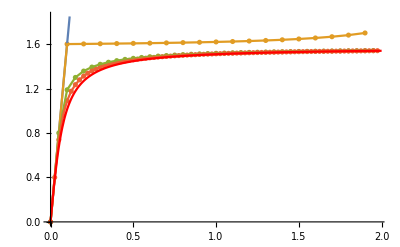

```mathematica
n10 = Import["./outputs/uloha1_eul_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_eul_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_eul_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_eul_80n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40, n80}],
ListLinePlot[{n10, n20, n40, n80}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### Taylor druheho radu

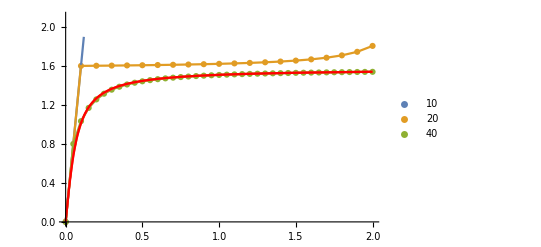

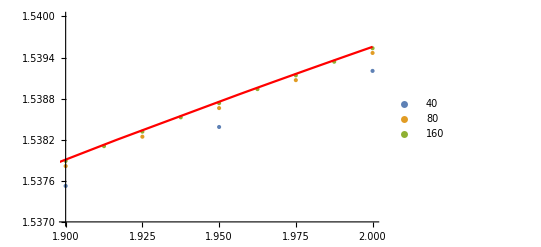

```mathematica
n10 = Import["./outputs/uloha1_tay_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_tay_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_tay_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_tay_80n.csv","CSV"];
n160 = Import["./outputs/uloha1_tay_160n.csv","CSV"];
n320 = Import["./outputs/uloha1_tay_320n.csv","CSV"];
n640 = Import["./outputs/uloha1_tay_640n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n10, n20, n40}, PlotLegends->{"10", "20","40"}],
ListLinePlot[{n10, n20, n40, n80}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n40, n80, n160}, PlotRange->{{1.9, 2}, {1.537, 1.54}},PlotLegends->{"40", "80", "160"}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 2

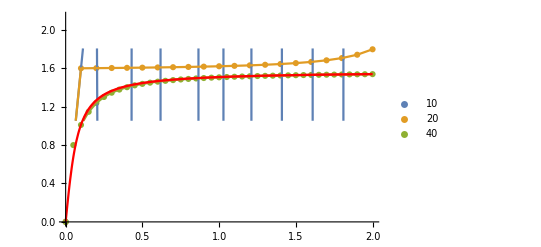

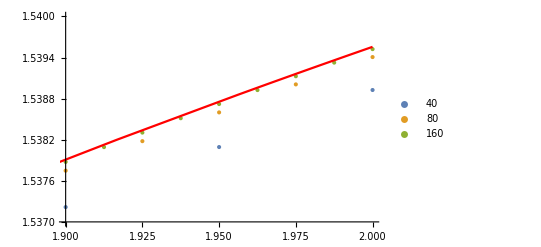

```mathematica
n10 = Import["./outputs/uloha2_tay_10n.csv","CSV"];
n20 = Import["./outputs/uloha2_tay_20n.csv","CSV"];
n40 = Import["./outputs/uloha2_tay_40n.csv","CSV"];
n80 = Import["./outputs/uloha2_tay_80n.csv","CSV"];
n160 = Import["./outputs/uloha2_tay_160n.csv","CSV"];
n320 = Import["./outputs/uloha2_tay_320n.csv","CSV"];
n640 = Import["./outputs/uloha2_tay_640n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n10, n20, n40}, PlotLegends->{"10", "20","40"}],
ListLinePlot[{n10, n20, n40, n80}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n40, n80, n160}, PlotRange->{{1.9, 2}, {1.537, 1.54}},PlotLegends->{"40", "80", "160"}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### Taylor 2 vs Taylor 3

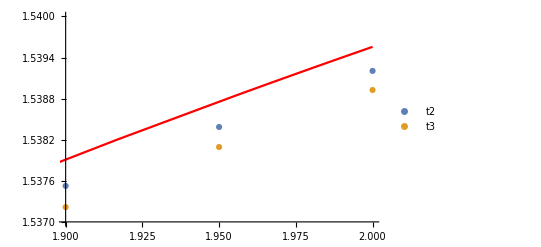

```mathematica
t2 = Import["./outputs/uloha1_tay_40n.csv","CSV"];
t3 = Import["./outputs/uloha2_tay_40n.csv","CSV"];DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{t2, t3}, PlotRange->{{1.9, 2}, {1.537, 1.54}},PlotLegends->{"t2", "t3"}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```